## Perturbation Theory: a matrix approach

Suppose we know the N eigenstates of an “unperturbed” Hamiltonian H^0.  Focus on a single one of the energy eigenstates φ_g^0, which for now we assume has no other eigenstates degenerate with it.  Now we add a small “perturbation” V:  H=H^0+V.  We want to know how E_m^0 and φ_g^0 change when we add V.

Rewrite the matrix representation in the H^0-basis as

H=(φ_g^0Hφ_g^0 | V^gk
V^kg | H^k)=(E_g^0+φ_g^0Vφ_g^0 | V^gk
V^kg | H^k)=(E_g^1 | V^gk
V^kg | H^k)

The V^gk matrix is 1× (N-1), a row vector, and V^kg=V^(gk †) is  (N-1)×1 (column vector), and H^k is (N-1)×(N-1) in size.  We shall see that to a good approximation we will only care about the diagonal elements H^(0 kk).

We can always write the (unnormalized) eigenvector we are after as φ_g=φ_g^0+∑_(k≠g) φ_k^0φ_k^0u_g=φ_g^0+χ_g:

φ^0φ_g= (1
χ_g)

The column vector χ_g is N-1 elements high.

The time-independent Schrödinger equation becomes

φ^0H φ_g=E_g φ^0φ_m→ (E_g^1 | V^gk
V^kg | H^(k k'))(1
χ_g)=E_g(1
χ_g)

Let’s write out the second “row” of this equation and solve for χ_g:

V^kg+H^(k k')χ_g=E_g χ_g→ χ_g=(E_g-H^(k k'))^-1 V^kg

Substitute this into the first row of (3) to get

E_g^1+V^kg χ_g=E_g→E_g^1+(V^gk(E_g-H^(k k')))^-1 V^kg=E_m

This equation is exact, but unfortunately not easily solved since the eigenvalue E_g appears on both sides of the equation and we also have to deal with the (N-1)×(N-1) matrix (E_g-H^k)^-1=(E_g-H^(0k)-V^k)^-1. Noting that (A+B)^-1=A^-1-A^-1 B (A+B)^-1, and picking A=E_g-H^(0 k), B=-V^k, we get

(E_g-H^k)^-1=(E_g-H^(0k))^-1+(E_g-H^k)^-1(V^k(E_g-H^k))^-1

We now substitute this into (5) to get

E_g =E_g^1+(V^gk(E_g-H^(0k)))^-1 V^kg+V^gk(E_g-H^k)^-1(V^k(E_g-H^k))^-1 V^kg

We have not made any approximations yet, but you can see that we have something that looks very much like a power series in V.  If we assume that each successive term is smaller than the previous one, then including the terms up to 2nd order in V we get

E_g ≃E_g^0+φ_g^0Vφ_g^0+(V^gk(E_g^0-H^(0k)))^-1 V^kg

Let’s write this out explicitly:

E_g ≃E_g^0+φ_g^0Vφ_g^0+∑_(k≠g) (E_g^0-E_k^0)^-1 φ_m^0Vφ_k^0φ_k^0Vφ_k^0

This is the main equation of perturbation theory.  It says that the primary effect of V on the energy is to change the energy by the expectation value of the perturbation.  If φ_g^0Vφ_g^0=0, then the change is “2nd order”.

Let’s now consider how the eigenstates are changed.  To first order in V,

φ_g=φ_g^0+χ_g=u_g^0+(E_g-H^k)^-1 V^kg u_g^0≃u_g^0+(E_m^0-H^(0k))^-1 V^kg u_g^0

Explicitly,

φ_g≃φ_g^0+∑_(k≠g) φ_g^0(φ_k^0Vu_g^0)/(E_g^0-E_k^0)

## Degenerate Perturbation Theory

It is straightforward now to deal the with problem of degenerate states.  The perturbation theory treated above tells us that problems will arise when the Bohr energies E_kg^0=E_k^0-E_g^0 become comparable to the matrix elements V_gk=φ_g^0Vφ_k^0.  Thus for degenerate perturbation theory we assume that there are a set of M “degenerate” states that violate the condition |V_gk/E_kg|<<1.  The Hamiltonian becomes

H=(H^g | V^gk
V^kg | H^k)

where H^g=H^(0g)+V^g is now an M×M matrix, V^gk is an M×(N-M) matrix, and H^k is (N-M)×(N-M).  We now write the wavefunction as

φ^0φ_g= (ϕ_g
χ_g)

where ϕ_gφ_g=1, ϕ_gχ_g=0, and proceed as before.  ϕ_g is a column vector of M elements, χ has N-M elements.  The second “row” of the Schrödinger equation becomes

χ_g≃(OverBar[E_g^0]-H^(0k))^-1 V^kg ϕ_g

where OverBar[E_g^0] is a average (or typical) unperturbed energy of the degenerate levels (if you care about the distinction between average or typical, then you probably shouldn’t be doing perturbation theory).

Now we write the first “row” of the Schrödinger equation:

H^g ϕ_g+V^gk χ_g=E_g ϕ_g

and substitute our approximate equation for χ_g to get

(H^g+V^gk(OverBar[E_g^0]-H^(0k))^-1 V^kg)ϕ_g=E_g ϕ_g

This shows that we can, to second order, simplify the Hamiltonian to an effective M×M Hamiltonian

H_eff^g=H^g+V^gk(OverBar[E_g^0]-H^(0k))^-1 V^kg

Most of the time, it is sufficiently accurate to simply approximate H_eff^g=H^g.

## Zeeman effect in 2p states of Hydrogen

As an example of degenerate perturbation theory, let’s consider the Zeeman effect in the 2p states of hydrogen.  The Hamiltonian in degenerate perturbation theory is

H_eff^g=E_(2p)+⟨ξ⟩L·S+μ_B B (L_z+2 S_z)

Degenerate perturbation theory tells us we don’t have to worry about admixtures of the other np states into the Hamiltonian.  The Hamiltonian commutes with J_z, so our states can be labelled by m_j, but the Zeeman part of the Hamiltonian has non-zero matrix elements between states 3/2 m_j and 1/2 m_j :

1/2 m_j L_z+2 S_z 3/2 m_j=∑_(m_l m_s) C_(1 m_l 1/2 m_s)^(1/2 m_j)(m_l+2 m_s)C_(1 m_l 1/2 m_s)^(3/2 m_j)

The Hamiltonian matrix for the m_j=1/2 states becomes (using ⟨L·S⟩_j=Piecewise[{{1/2, j==3/2}, {-1, j==1/2}}])

```mathematica
Heff=({{ξ/2, 0}, {0, -ξ}})+μB With[{mj=1/2},Table[Sum[ClebschGordan[{1,ml},{1/2,ms},{j,mj}]ClebschGordan[{1,ml},{1/2,ms},{jp,mj}](ml+2 ms),{ml,-1,1},{ms,-1/2,1/2}],{j,{3/2,1/2}},{jp,{3/2,1/2}}]];Heff//MF
```

((2 μB)/3+ξ/2 | -(√2 μB)/3
-(√2 μB)/3 | μB/3-ξ)

The eigenvalues are

```mathematica
Eigenvalues[Heff]
```

{1/4 (2 μB-ξ-√(4 μB^2+4 μB ξ+9 ξ^2)),1/4 (2 μB-ξ+√(4 μB^2+4 μB ξ+9 ξ^2))}

Defining a scaled field by B=b B_s=b ξ/μ, we can plot the energies

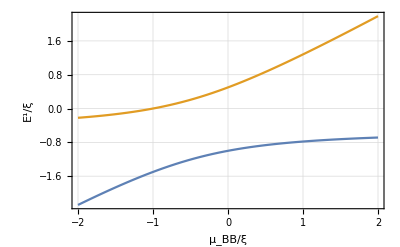

```mathematica
degplot=ThadPlot[Eigenvalues[Heff]/.{ξ->1,μB-> b},{b,-2,2},PlotRange-> All,{"μ_BB/ξ","E^1/ξ"}]
```

Our 1st order non-degenerate perturbation result for m_j=1/2 was E_j=Piecewise[{{ξ/2+2/3 μ_B B, j==3/2}, {-ξ+1/3 μ_B B, j==1/2}}]

Show both on the same plot:

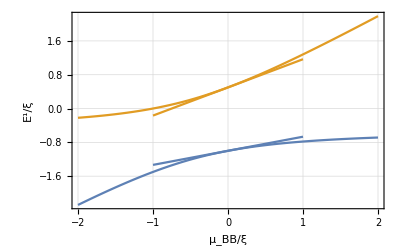

```mathematica
Show[degplot,Plot[Evaluate[{-1+1/3 b,1/2+2/3 b}],{b,-1,1}]]
```

As long as μ_B B<<ξ, the first-order perturbation and degenerate perturbation result agree well.